# Lista 5

## Zadanie 1

Mając dowolny zbiór danych empirycznych (geograficznych, ekonomicznych, społecznych itd.) można się zastanowić, czy nie opisuję ich prawo Benford’a, które mówi, że prawdopodobieństwo pojawienia się cyfry K na pierwszym miejscu liczby empirycznej wynosi log_10(1 + 1/ K ). Sprawdź, jak się ta reguła ma do:

a) pomiaru prędkości wiatru w stolicach Europy 

oraz 

b) populacji we wszystkich krajach świata. 

Wyniki nanieś na jeden wykres (ListPlot) i odpowiednio go zredaguj. 

UWAGA, można korzystać np. z funkcji:
IntegerDigits lub RealDigits, WeatherData[miasto,”WindSpeed”], CountryData[“kraj”,”Population”], CountryData[“Europe”].

## Zadanie 2

Używając funkcji Map pomnóż obydwie strony równania

x^2/(x-1) == 1/(1-x) 

przez (1-x)^2 i dokonaj uproszczenia tylko lewej strony.

## Zadanie 3

Narysuj fraktal według przepisu. 

a) w pierwszym kroku jest to odcinek o długości 1.

b) w drugim kroku odcinek jest dzielony na trzy równe części, pierwsza i ostatnia część odcinka pozostaje na miejscu, a odcinek środkowy zastąpiony jest połączonymi ze sobą odcinkami o tej samej długości co odcinek usunięty - nowe odcinki tworzą ramiona trójkąta równobocznego.

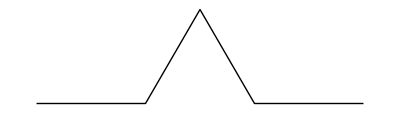

c) w trzecim kroku każdy z odcinków jest modyfikowany zgodnie z procedurą z punktu b).

Poniżej przedstawione są trzy kolejne kroki iteracji:

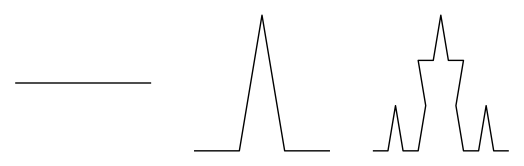

Wykonaj rysunek dla 10 kolejnych kroków.

Podpowiedź: skorzystaj z funkcji Line, Graphics, Flatten, Partition, Map.